```mathematica
g=CompleteKaryTree[3,8]
```

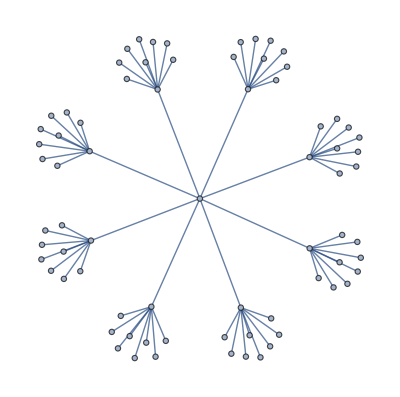

Set::write: Tag Inherited in Inherited["State"] is Protected.

```mathematica
g=CompleteKaryTree[4,8]
```

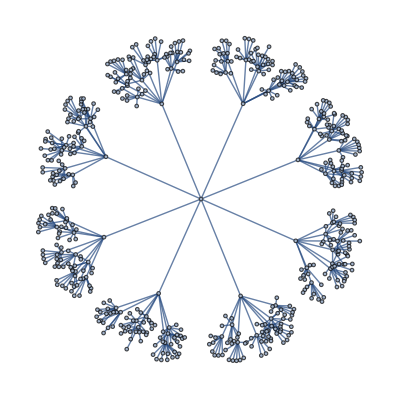

Set::write: Tag Inherited in Inherited["State"] is Protected.

```mathematica
g=CompleteKaryTree[5,8]
```

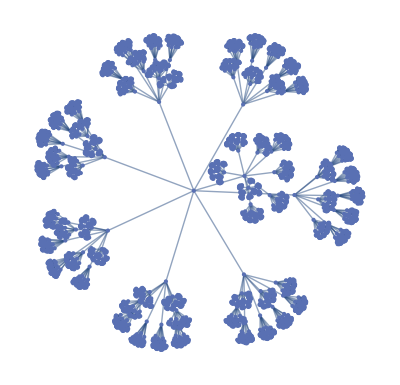

Set::write: Tag Inherited in Inherited["State"] is Protected.

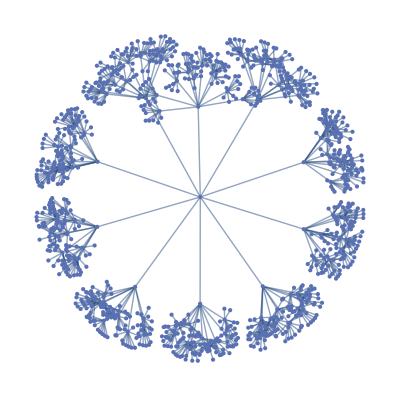

```mathematica
g=CompleteKaryTree[4,10]
```

```mathematica
g=CompleteGraph[15]
```

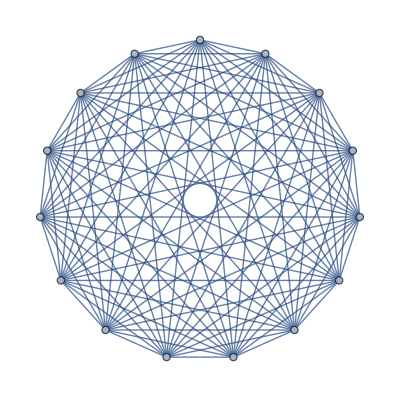

Set::write: Tag Inherited in Inherited["State"] is Protected.

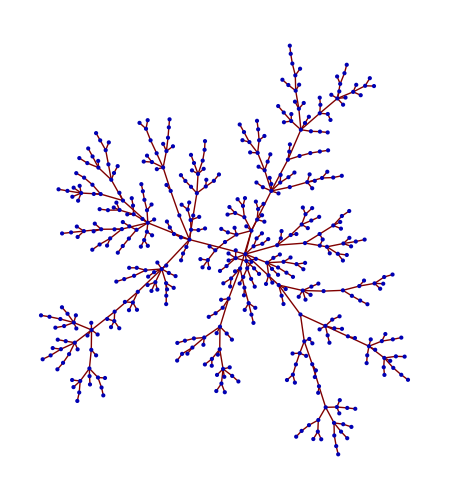

```mathematica
g=RandomInteger[#]->#+1&/@Range[0,500];
GraphPlot[g,Method->{"SpringElectricalEmbedding","RepulsiveForcePower"->-2}]
```

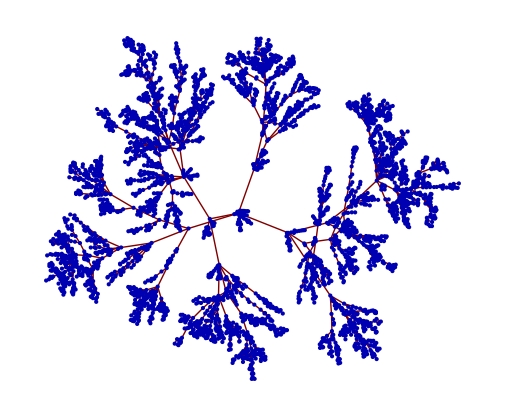

```mathematica
g=RandomInteger[#]->#+1&/@Range[0,4000];
GraphPlot[g,Method->{"SpringElectricalEmbedding","RepulsiveForcePower"->-1}]
```

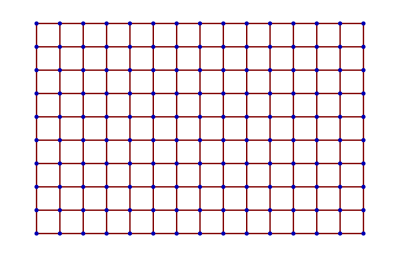

```mathematica
GraphPlot[GridGraph[{10,15}],Method->"SpringElectricalEmbedding"]
```

```mathematica
g=CompleteGraph[15]
EdgeDelete[g,1->2]
```

-Graphics-

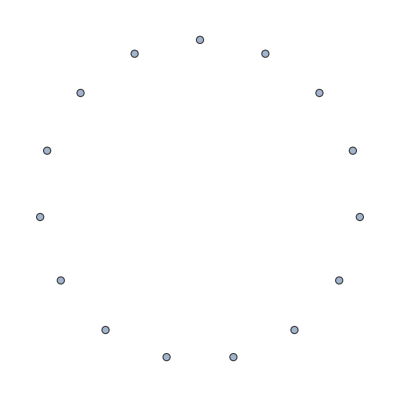

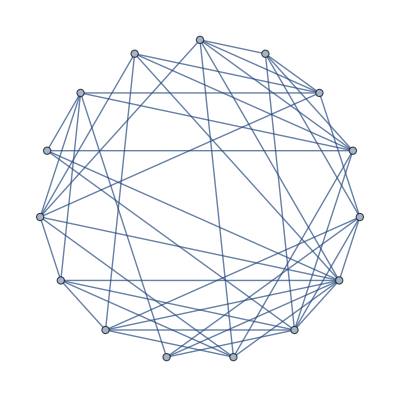

-Graphics-

```mathematica
v=15;

p=0;
g=CompleteGraph[v];
list=Flatten[Table[If[Random[]>p,i->j,Nothing],{i,1,v},{j,i+1,v}]];
g=EdgeDelete[g,list]

p=0.5;
g=CompleteGraph[v];
list=Flatten[Table[If[Random[]>p,i->j,Nothing],{i,1,v},{j,i+1,v}]];
g=EdgeDelete[g,list]

p=1;
g=CompleteGraph[v];
list=Flatten[Table[If[Random[]>p,i->j,Nothing],{i,1,v},{j,i+1,v}]];
g=EdgeDelete[g,list]
```

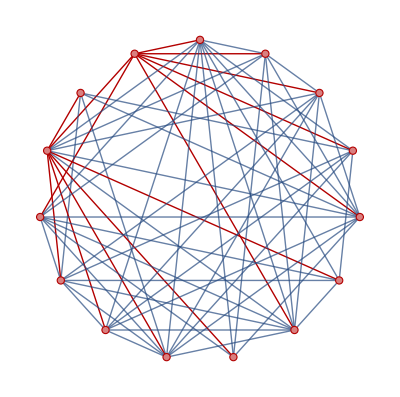

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
p=0.6;
v=15;
g=CompleteGraph[v];
list=Flatten[Table[If[Random[]>p,i->j,Nothing],{i,1,v},{j,i+1,v}]];
g=EdgeDelete[g,list];
mst=FindSpanningTree[g];
HighlightGraph[g,mst,GraphHighlightStyle->"Thick"]
```